```mathematica
(*PROBLEM 2a*)
```

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m
```

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m;
FullForm[%]
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
(*Types of groupings for operators*)
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a*a*a*b*b*c
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b) (*Superscripts are interperaed as power*)
```

x^(a+b)

```mathematica
∂_x x^n (*TWO-D Operator*)
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
(*PROBLEM 2b*)
```

```mathematica
Factor[x^6-1]
```

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
List[a,b,c] (*list is just a tag not an opernad*)
```

{a,b,c}

```mathematica
(*PROBLEM 2C*)
```

```mathematica
(*When the expressions you type in are complicated,it is often a good idea to put extra space inside each set of brackets.This makes it somewhat easier for you to see matching pairs of brackets.*)
```

```mathematica
(term)  (* parentheses for grouping*)
f[x] (*square brackets for functions*)
{a,b,c}(* curly braces for lists*)
v[[i]] (*double brackets for indexing (Part[v,i])*)
```

term

f[x]

{a,b,c}

Part::pspec: Part specification i is neither an integer nor a list of integers.

v⟦i⟧

```mathematica
(*PROBLEM 2D*)
```

```mathematica
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5} (*List*)
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"} (*anything can go in a list*)
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
Range[10] (*Square brackets*)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]] (*Part function*)
```

9

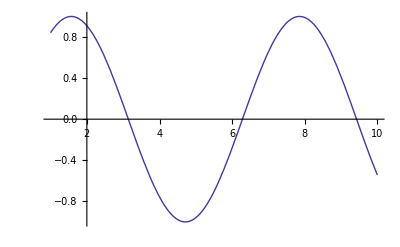

```mathematica
(*Making Plots*)
Plot[Sin[x],{x,1,10}]
```

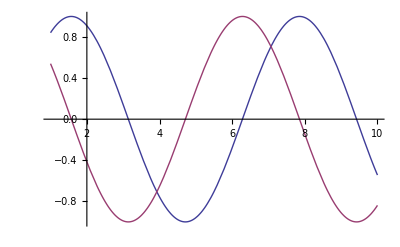

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*QUESTION 3a*)
```

```mathematica
3 x-x+2 (*Can do symbolic analysis*)
```

2+2 x

```mathematica
x^2+x-4 x^2 (*Mathematica does basic algebra*)
```

x-3 x^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
(x+2 y+1) (x-2)^2;
Expand[%]
```

```mathematica
4-3 x^2+x^3+8 y-8 x y+2 x^2 y
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Log[1+Cos[x]] (*Mathematica doesn't know rules for this function*)
```

Log[1+Cos[x]]

```mathematica
(*PROBLEM 3B*)
```

```mathematica
1+2 x/.x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
x+5-2 x
```

5-x

```mathematica
x=.
```

```mathematica
x+5-2 x
```

5-x

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
t/.x->Pi//N
```

10.8696

```mathematica
(*Problem 3c*)
```

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Expand[(1+x)^2];
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
(*PROBLEM 3d*)
```

```mathematica
Simplify[x^2+2 x+1]
```

(1+x)^2

```mathematica
Simplify[x^10-1]
```

-1+x^10

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
Integrate[1/(x^4-1),x];
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[x^2+2 x+1];
D[%,x];
Simplify[%]
```

2 (1+x)

```mathematica
Simplify[Gamma[x] Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
(*PROBLEM 4a*)
```

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}]
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x^2+y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
D[x^2+y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
D[x^2+y^2,{{x,y}}]  (*gives gradient*)
```

{2 x,2 y}

```mathematica
D[x^2+y^2,{{x,y},2}] (*Hessian*)
```

{{2,0},{0,2}}

```mathematica
D[{x^2+y^2,x y},{{x,y}}] (*Jacobian*)
```

{{2 x,2 y},{y,x}}

```mathematica
(*PROBLEM 4b*)
```

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[1/(x^4-a^4),x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
Integrate[Sin[x]^2,{x,a,b}]
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

```mathematica
Integrate[x^10 Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

(21 π)/512